```mathematica
(* Que: Maximize x+(y/2)
s.t. 3x+2y≤12
	 x≤2
		 x+y≥8
	 -x+y≥4
	 x≥0 && y≥0
*)

Maximize[{ x+(y/2),3 x+2 y≤12 && x≤2 && x+y≥8 && -x+y≥4 && x≥0 && y≥0},{x,y}]
```

Maximize::infeas: There are no values of {x,y} for which the constraints 3 x+2 y≤12&&x≤2&&x+y≥8&&-x+y≥4&&x≥0&&y≥0 are satisfied and the objective function x+y/2 is real valued.

{-∞,{x→Indeterminate,y→Indeterminate}}

```mathematica
RegionPlot[{ 3 x+2 y≤12 && x≤2 && x+y≥8 && -x+y≥4 && x≥0 && y≥0},{x,-5,5},{y,-5,5},Frame->False,Axes->True]
```

-Graphics-

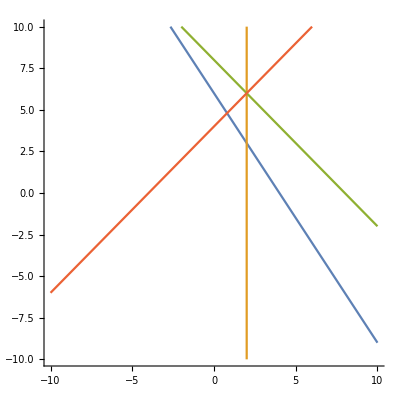

```mathematica
ContourPlot[{3 x+2 y==12,x==2,x+y==8,-x+y==4,x==0 && y==0},{x,-10,10},{y,-10,10},Frame->False,Axes->True]
```